On p17 of TAOCP F6. Donald Knuth shows a sequence of frames from Conways game of Life that end with the alive cells forming the letters LIFE.

In the next few paragraphs he describes how this is achieved.

He states that 190 clauses are needed for each cell for each transition T.

He does not provide these clauses.

I am exploring this section as part of an undergrad math project. I would love to be able to code up this example and get the game of life to write other words besides LIFE.

I wish Knuth had provided these clauses as I find it difficult to infer them from his implicit description of them.

Has anyone managed to write these clauses down?

Here are screen shots of the section: and a link to a pdf of a preprint of the book.

## using a SAT solver to make Conways Game of Life write Characters and Words!

Here I have tried to formulate a simpler version of the problem Knuth describes

```mathematica
life44
```

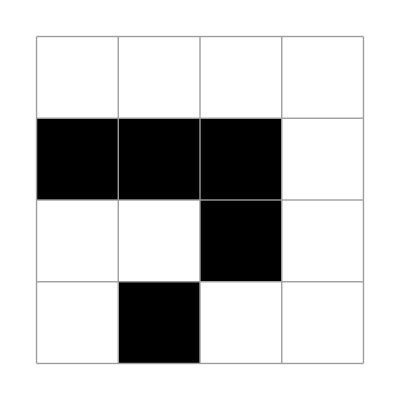
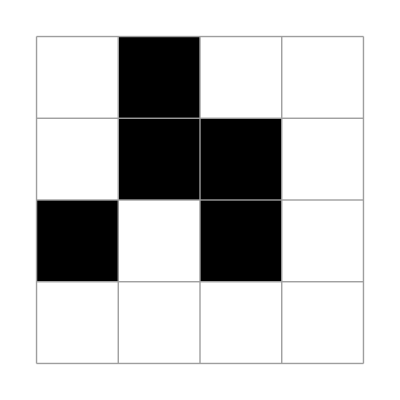
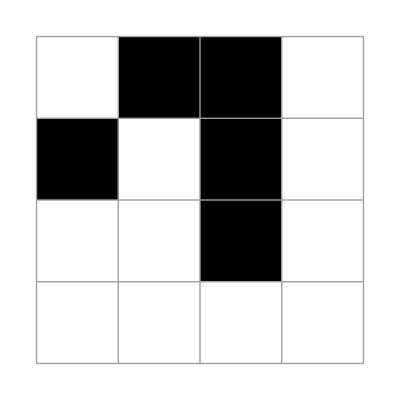
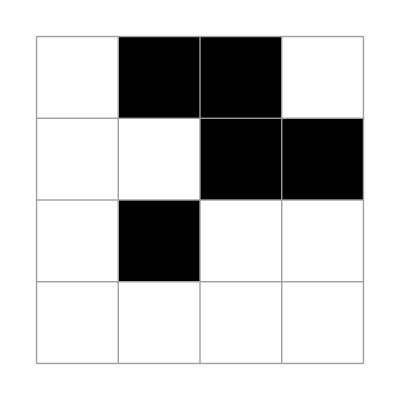

```mathematica
X1=({{0, 0, 0, 0}, {1, 1, 1, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}});
plt/@NestList[updateLife[{4,4}][ #]&,
X1,3]
```

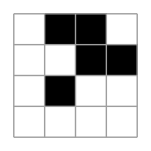
find a sequence that ends in -Graphics-

(x_411 | x_412 | x_413 | x_414
x_421 | x_422 | x_423 | x_424
x_431 | x_432 | x_433 | x_434
x_441 | x_412 | x_413 | x_444)=(0 | 0 | 0 | 0
1 | 1 | 1 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0)